```mathematica
(*
https://class.coursera.org/compfinance-009/quiz/attempt?quiz_id=35
*)
```

```mathematica
dist=NormalDistribution[0.05,0.10]
```

NormalDistribution[0.05,0.1]

```mathematica
1-CDF[dist,0.10]
```

0.308538

```mathematica
CDF[dist,-0.10]
```

0.0668072

```mathematica
CDF[dist,0.15]-CDF[dist,-0.05]
```

0.682689

```mathematica
Quantile[dist,0.01]
```

-0.182635

```mathematica
Quantile[dist,0.05]
```

-0.114485

```mathematica
Quantile[dist,0.95]
```

0.214485

```mathematica
Quantile[dist,0.99]
```

0.282635

```mathematica
msft=NormalDistribution[0.05,0.10]
sbux=NormalDistribution[0.025,0.05]
```

NormalDistribution[0.05,0.1]

NormalDistribution[0.025,0.05]

```mathematica
r=NormalDistribution[0.04,0.09]
```

NormalDistribution[0.04,0.09]

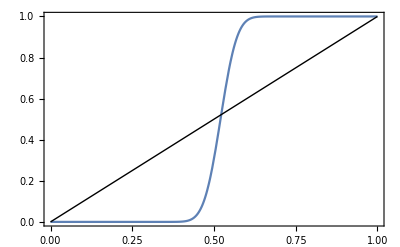

```mathematica
ProbabilityPlot[msft]
```

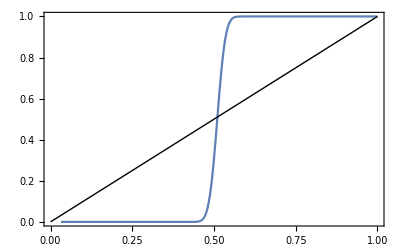

```mathematica
ProbabilityPlot[sbux]
```

```mathematica
range=Range[-0.25,0.35,0.01];
```

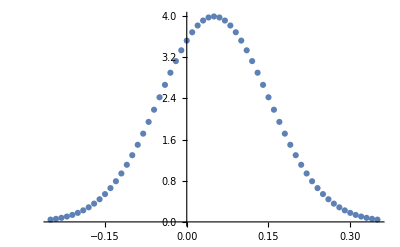

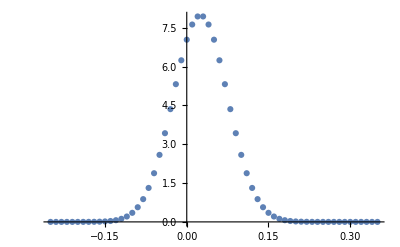

```mathematica
ListPlot[Transpose[{range,PDF[msft,#]&/@range}]]
ListPlot[Transpose[{range,PDF[sbux,#]&/@range}]]
```

```mathematica
dist2=NormalDistribution[10500,1000]
```

NormalDistribution[10500,1000]

```mathematica
N@CDF[dist2,9000]
```

0.0668072

```mathematica
CDF[dist2,10500]
Quantile[dist,0.05]
```

1/2

-0.114485

```mathematica
8855.146373048527/10000-1
```

-0.114485

```mathematica
CDF[msft,0.05]
Quantile[msft,0.05]
CDF[msft,-0.1]
```

0.5

-0.114485

0.0668072

```mathematica
(* Quiz 2 Question 9 *)
d=NormalDistribution[0.04,0.09];
Quantile[d,0.01]
Quantile[d,0.05]
```

-0.169371

-0.108037

```mathematica
(* Quiz 2 Question 10 *)
(E^Quantile[d,0.01])-1
(E^Quantile[d,0.05])-1
```

-0.155805

-0.102405

```mathematica
(* Quiz 2 Question 11 *)
41.29/38.23-1
41.74/41.11-1
```

0.0800419

0.0153247

```mathematica
(* Quiz 2 Question 12 *)
Log[41.29/38.23]
Log[41.74/41.11]
```

0.0769998

0.0152085

```mathematica
(* 13 *)
(41.29+0.1)/38.23-1
0.1/38.23
```

0.0826576

0.00261575

```mathematica
(* 14 *)
r=41.29/38.23
r^12-1
Log[r^12]
```

1.08004

1.51934

0.923998

```mathematica
p=41.29/38.23*8000+41.74/41.11*2000
p/10000-1
```

10671.

0.0670984